```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
(*All calculation results stored in results and sols lists*)
results={};
sols={};
(*List of δ values to compute, where δ==1-q/k*)
δvec=(Table[10^eδ,{eδ,-10,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/10}]~Join~Table[δ,{δ,1,2,1/5}])//Reverse;
δvec={1/10}//Reverse;
δvec=(Table[10^eδ,{eδ,-3,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/5}])//Reverse;
(*List of Subscript[f, 0] values to compute, where f(Subscript[z, H])==Subscript[f, 0] counts as hitting the horizon*)
f0vec=Table[E^eδ,{eδ,-10,-10}]//Reverse;
f0vec={10^-15}//Reverse;
(*Loop over Subscript[f, 0] values*)
For[if0=1,if0≤Length[f0vec],if0+=1,
fixf0results={};
f0=f0vec[[if0]];
For[iδ=1,iδ≤Length[δvec],iδ+=1,
(*Loop over δ values*)
δ=δvec[[iδ]];
ϵ=10^-40;λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0];q=k(1-δ);
(*Define potentials and their derivatives*)
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-E^(-a ϕ));
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
(*Define equations to solve*)
eqn1=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z]==1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z]==1/(q z+1)dςdG[ϕ[z],G[z]];
(*Define initial conditions*)
ic1=ϕ[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,0}]/.z->ϵ;
ic2=ϕ'[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,1}]/.z->ϵ;
ic3=G[ϵ]==D[√(24λ)(z+1/k),{z,0}]/.z->ϵ;
ic4=G'[ϵ]==D[√(24λ)(z+1/k),{z,1}]/.z->ϵ;
ic5=f[ϵ]==1;
ic6=β[ϵ]==Ω[ϕ[ϵ],G[ϵ]]+q E^(-a ϕ[ϵ]);
(*The exact solutions, if you want to compare*)
ϕExact[z_]:=√(8/3)λ(z+1/k)^2;
GExact[z_]:=√(24λ)(z+1/k);
fExact[z_]:=1;
βExact[z_]:=k ((U[GExact[z]]+1-a ϕExact[z])-E^(-a ϕExact[z]))+q E^(-a ϕExact[z]);
(*factor=1-f0;
f0=E^-50;*)
(*SOLVE EQUATIONS HERE; RETURN SOLUTIONS AND VALUE OF Z==Subscript[Z, H] WHERE F(Subscript[Z, H])==Subscript[F, 0]*)
tmp=Reap[NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,100k},AccuracyGoal->∞,WorkingPrecision->100,MaxSteps->∞,Method->{"EventLocator", "Event"->f[z]-f0, "EventAction":>Sow[z]}]];
(*Store the solutions for this value of δ*)
sol=First[{ϕ,G,f,β}/.First[tmp]];
(*Range of solutions defines range of z*)
{zmin,zmax}=First[sol[[1]]["Domain"]];
(*Define Subscript[z, H]*)
zH=tmp[[2,1,1]];
(*Compute the function A by integrating the solution for β appropriately*)
A[z_]:=NIntegrate[(sol[[4]][zp])/(q zp+1),{zp,ϵ,z},MaxRecursion->1000000,Method->{"GlobalAdaptive",MaxErrorIncreases->10000},WorkingPrecision->50];
(*Define the entropy density s in units of 8 π M^3*)
coeff=Exp[-3A[zH]];
(*zHest=factor zH;
coeffest=Exp[-3A[zHest]];*)
(*Add the solutions sol={ϕ,G,f,β} to the total list of sols*)
AppendTo[sols,sol];
(*Print the results: q/k, Subscript[z, H], k Subscript[z, H], T at horizon (version 1), T at horizon (version 2)*)
(*T at horizon (version 1): just use the NDSolve solution to estimate T at the horizon*)
(*T at horizon (version 2): estimate where the slope of f(z) looks linear by f''(z)==0, and take this to be the slope at the horizon*)
Print[{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],-1/(4π)sol[[3]]'[z]/.FindRoot[sol[[3]]''[z],{z,999/1000 zH},WorkingPrecision->30],coeff}];
AppendTo[fixf0results,{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],-1/(4π)sol[[3]]'[z]/.FindRoot[sol[[3]]''[z],{z,999/1000 zH},WorkingPrecision->30],coeff}]];
(*Append the results from this loop to the total list of results*)
AppendTo[results,fixf0results]]
```

NDSolve::ndsz: At z == 0.0001639744620302871398859261318243238406671148966483803844117458232055659933934511538032188856207903281, step size is effectively zero; singularity or stiff system suspected.

{1/10,0.0001639744620302869737992310025292570510317285167008377727870963441821030582885197982591920784158529879,0.129647154488048633640092778650818595517818346094268373865983905815945811604733391258712296123450957,483.78797210777670684106380630822175538423753305315624150956870555216537810381008569,639.87041127245948761462508,0.152568027242572695192462839874048056913929510043}

NDSolve::ndsz: At z == 0.0002008800936505836597942727394816208987616438941302898856877348622854853854214035602934997452305251431, step size is effectively zero; singularity or stiff system suspected.

{3/10,0.0002008800936505834847427688320612844453058459480497513031011008994987132037978284801913364640650645416,0.1588267600492599423667257566674404255252932404245994941653145361977503137278303679828650458939547758,458.26924617667963677842597139386042413879294244354581077939939177529783378427391792,576.360312434243730211528449,0.1034279161051623582887075078596071635574826708186}

NDSolve::ndsz: At z == 0.0002532165041578182452749988525441253206987078177343426636183494634015619643981690558298461565799760005, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

{1/2,0.0002532165041578180601826452399106503265718985412657112894326043751150367998044400387584971396996673463,0.2002067811474727673555822899711972741630574837900973899762555675346106191828196268465821146655276209,432.83283197646876589104215375575587361762924416283458706901059230442230214953451014,522.65586265527809660414108,0.0637301024269152949734589345764766940218356594778}

{7/10,0.0003391069689101459195116265389849076628097216237522286260998897561615920298467949958604358187847381535,0.2681164679055154124258013009491696249303721860530876358661265902075532736421042663942847451051286916,400.11632068131593172647500761998346826648798324165679470080479465131850688380087423,475.4858611986485155174392,0.03237831436203895054576826590245581859623803959339}

{9/10,0.0005453009565735106096595989199672735170828447060781421017201999142904567511908904870329854358203409492,0.431144682434198573000635837247210657376053893804095708271638889143359651907295482124345934915085554,336.62327181469280879687212350836222152864648723676050858534431213494971716713210067,431.9528216872783535029802,0.008674971129533361540207836867480155401778749280882}

{99/100,0.001015397802053368718774917493074948410423766362808008006192705345257096212344142334679685484600660932,0.8028288922534953203270589417743014517168183028911023065326906580368440400776623027621161209684674986,239.48576489222862461808227848241902828603142605107741192809814551471748971469280699,421.2283342362293475343781,0.000707551004562248395083701457892293797408650184833}

{999/1000,0.001468536484872363155557046427375874593563093261581857913960205500928273171339313454365702715863417403,1.161105053605340098193536542365979807630060399344036157126144998243968406562357776570460216244768149,187.7441794982973137010531908471662908116918053265973691788580420216814385788513757,440.564382464991275442057,0.0000644133832145925740360107594941217710800990098998}

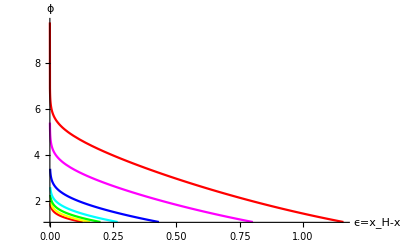

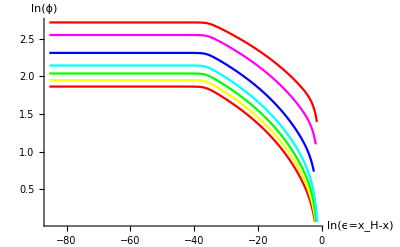

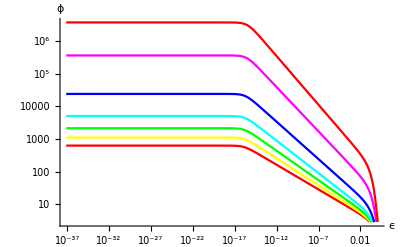

```mathematica
(*Makes a nice set of rainbow colors for viewing sets of curves at once*)
plotStyles=Table[Hue[Rescale[i,{1,Length[results[[1]]]}]],{i,Length[results[[1]]]}];
(*Define list of Subscript[z, H] values computed above*)
zHlist=results[[;;,;;,2]][[1]];
ϕlist=Table[sols[[i]][[1]],{i,Length[sols]}];
Glist=Table[sols[[i]][[2]],{i,Length[sols]}];
flist=Table[sols[[i]][[3]],{i,Length[sols]}];
βlist=Table[sols[[i]][[4]],{i,Length[sols]}];
(*Do a linear-linear plot of ϕ*)
Show[Table[Plot[ϕlist[[i]][zHlist[[i]]-x/q]//Evaluate,{x,q ϵ,q zHlist[[i]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
(*Use my own make-shift log-log routine*)
Show[Table[Plot[Log[ϕlist[[i]][zHlist[[i]]-E^lnx/q]]//Evaluate,{lnx,Log[q ϵ],Log[q zHlist[[i]]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(ϕ)",16]},WorkingPrecision->100,PlotPoints->200],{i,Length[sols]}],PlotRange->All]
(*Use Mathematica's LogLogPlot routine*)
Show[Table[LogLogPlot[ϕlist[[i]][zHlist[[i]]-x/q]//Evaluate,{x,q ϵ,q zHlist[[i]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ϵ",16],Style["ϕ",16]},WorkingPrecision->100,PlotPoints->200],{i,Length[sols]}],PlotRange->All]
```

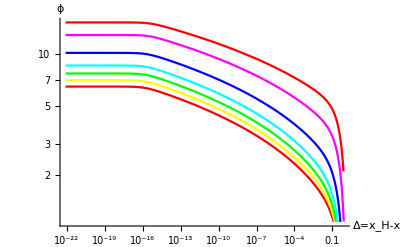

```mathematica
(*Define corresponding list of x-coordinates of horizon locations*)
xHlist=q zHlist+1;
(*Set lists of points in z and x for checking/fitting log-log plots and slopes*)
(*Spaces z-points logarithmically leading up to horizon Subscript[z, H]*)
zpts=Table[zHlist[[i]]-PowerRange[10^-25,zHlist[[i]],1+10^-2],{i,Length[zHlist]}];
(*Convert to xpts*)
xpts=q zpts+1;
(*Defined Δ==Subscript[x, H]-x for convenience*)
Δpts=Table[xHlist[[i]]-xpts[[i]],{i,Length[xHlist]}];
(*Evaluate ϕ-solutions at z-points*)
ϕpts=Table[ϕlist[[i]]/@zpts[[i]],{i,Length[zHlist]}];
(*Check that the plot looks right*)
Show[Table[ListLogLogPlot[{Δpts[[i]],ϕpts[[i]]}//Transpose,PlotStyle->plotStyles[[i]],AxesLabel->{Style["Δ=x_H-x",16],Style["ϕ",16]},Joined->True],{i,Length[sols]}],PlotRange->All]
```

{-0.999994089377426140002125444262855001512162015652900370381664766377853494944084119,-1.00000769243438354330136028231862895325162515118326769900706459556432630135216573,-1.0000058822267239954911186978549021578838191792016563231837882170462536378978945,-0.999986661706776111003457522217484391383953950647373287060880251408075975945491,-1.00000008701250241744651538757212951765949145701400319562979493063981552992316321,-0.99999205115417424242884329913449423076787081448093045556432514875548750576275894,-0.99998561521910669626153643182640123841832495482590337825146519291508779453018444}

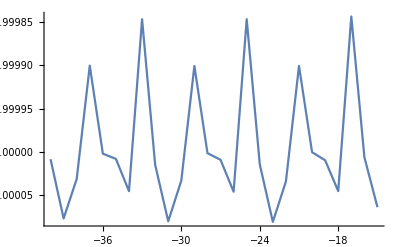

```mathematica
ϵpts=Table[E^lnϵ,{lnϵ,-40,-15}];
ϕpts=Table[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
ϕppts=-q^-1 Table[sols[[i]][[1]]'[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
ϕpppts=q^-2 Table[sols[[i]][[1]]''[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
Table[Mean[(ϵpts*ϕpppts[[i]])/ϕppts[[i]]],{i,Length[sols]}]
ListLinePlot[{Log[ϵpts],(ϵpts*ϕpppts[[1]])/ϕppts[[1]]}//Transpose]
```

{-0.99395604643906566372661163116720849411482770674745159180617610844245743695641,-0.99381785455485532518549450830294447985376313205008078848053969750878781436221,-0.9936152894559246102624551326523550414671195047310937617252479788388837918281,-0.9931850198864278343333664872657292934357579399879446981659468573142072671823,-0.9917591564581469283413162542542675191073377322315455579037940492267919306618,-0.9872567403148367461928098071352867811832688474429000889590226952355846534141,-0.9825777998089626126846515693615852169628846440342486559941397592533900710179}

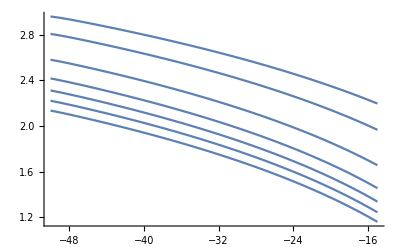

```mathematica
ϵpts=Table[E^lnϵ,{lnϵ,-50,-15}];
lnϕpts=Table[Log[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-#/q]]&/@ϵpts,{i,Length[sols]}];
ϕppts=-q^-1 Table[sols[[i]][[1]]'[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
ϕpppts=q^-2 Table[sols[[i]][[1]]''[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
Table[Mean[(ϵpts*ϕpppts[[i]])/ϕppts[[i]]],{i,Length[sols]}]
Show[Table[ListLinePlot[{Log[ϵpts],lnϕpts[[i]]}//Transpose],{i,Length[sols]}],PlotRange->All]
```

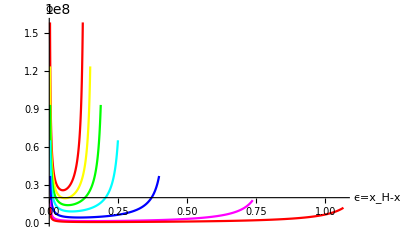

```mathematica
Show[Table[Plot[(results[[;;,;;,2]][[1,i]]-x/q)^-1(sols[[i]][[1]]'[results[[;;,;;,2]][[1,i]]-x/q])/(sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-x/q])//Evaluate,{x,q ϵ,q results[[;;,;;,2]][[1,i]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

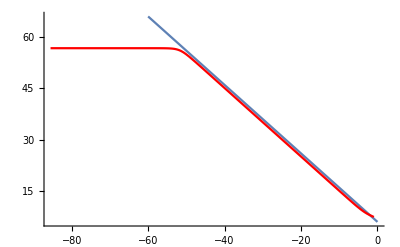

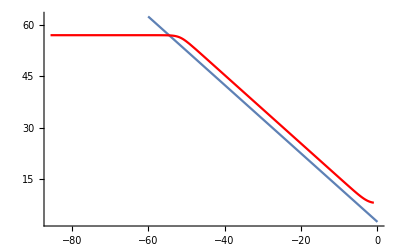

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All];
Show[Plot[8.725+0.02x,{x,-60,0}],Table[Plot[Log[sols[[i]][[3]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|f'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All];
Show[Plot[11.4-0.98x,{x,-60,0}],Table[Plot[Log[sols[[i]][[3]]''[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|f'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All];
Show[Plot[6-x,{x,-60,0}],Table[Plot[Log[sols[[i]][[1]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Plot[√6-x,{x,-60,0}],Table[Plot[Log[sols[[i]][[2]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

```mathematica
k//N
q//N
```

790.655

79.0655

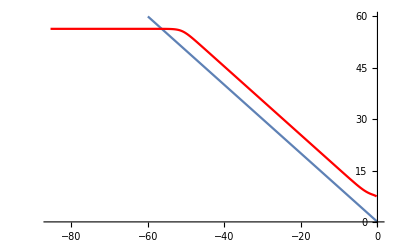

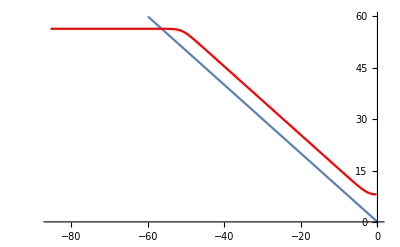

```mathematica
Show[Plot[-1x,{x,-60,0}],Table[Plot[Log[sols[[i]][[1]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|ϕ'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Plot[-1x,{x,-60,0}],Table[Plot[Log[sols[[i]][[2]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|G'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

```mathematica
Plot[1/2-6.5^-1 x,{x,-60,0}]
Plot[3-4^-1 x,{x,-60,0}]
```

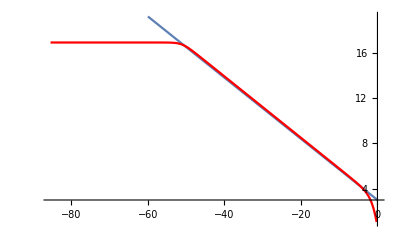

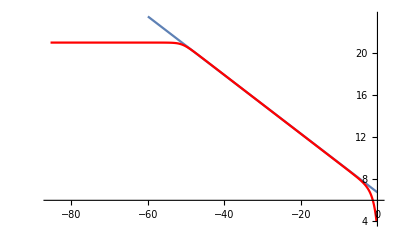

```mathematica
Show[Plot[3-3.7^-1 x,{x,-60,0}],Table[Plot[sols[[i]][[1]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Plot[6.75-3.6^-1 x,{x,-60,0}],Table[Plot[sols[[i]][[2]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["G",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

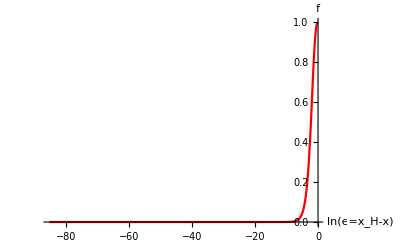

```mathematica
Show[Table[Plot[sols[[i]][[3]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],PlotRange->All,AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["f",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

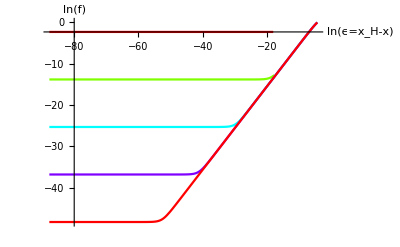

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

```mathematica
E^-18.
```

1.523×10^-8

```mathematica
q zH+1
```

1.01296471544880487649558269576245106010638880167059

```mathematica
ListLinePlot[Table[results[[i,;;,{1,3}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["z_H",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,4}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{4,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{5,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
```

```mathematica
Export["stable_zH_vs_qByk.pdf",%]
Export["unstable_T_vs_qByk.pdf",%]
Export["stable_s_vs_qByk.pdf",%]
Export["unstable_s_vs_T.pdf",%]
Export["stable_T_vs_qByk.pdf",%]
Export["stable_s_vs_T.pdf",%]
```

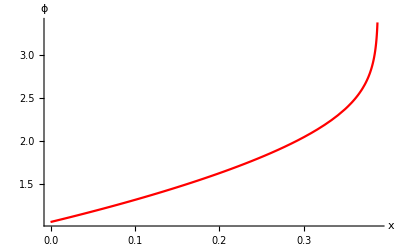

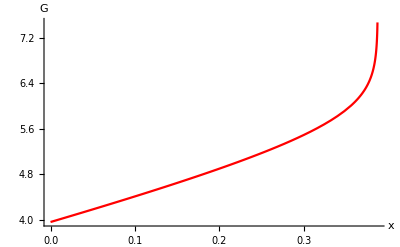

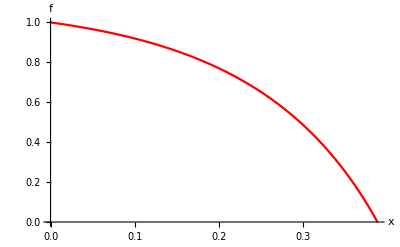

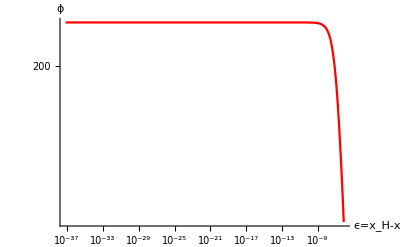

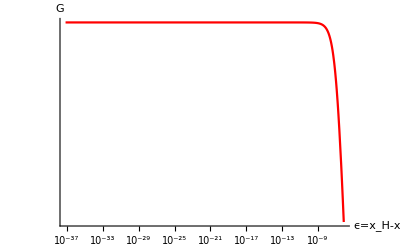

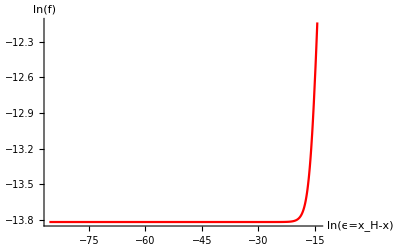

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[sols]}]],{i,Length[sols]}];
plotLegends=Table[StringForm["q/k=``",results[[;;,;;,1]][[1,i]]],{i,Length[sols]}];
Show[Table[Plot[sols[[i]][[1]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["ϕ",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[sols[[i]][[2]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["G",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[sols[[i]][[3]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["f",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[LogLogPlot[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[LogLogPlot[sols[[i]][[2]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["G",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[1,i]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[1,i]]-1]},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```